```mathematica
fnoise[x_] := RandomInteger[{1,256}]/256 * x;
anzahlInput = 3; anzahlOutput = 1;


l = 5; (*Anzahl Sektoren*)
modulo[z_] := Exp[I Mod[Arg[z],2 Pi/l]];
toComplex[x_] := Exp[I 2 Pi /l x];
toReal[z_] := Arg[z] / ((2 Pi)/l);
round[z_] := z /modulo[z];
Activ[z_] := toReal[modulo[z]];
```

```mathematica
weights = Table[N[Exp[I   RandomInteger[{1,256}]/256]],{anzahlOutput},{anzahlInput}]
```

{{0.934736+0.355343 ⅈ,0.994025+0.109157 ⅈ,0.813242+0.581925 ⅈ}}

```mathematica
in= {{0.1,0.1,1},{0.1,0.9,1},{0.9,0.1,1},{0.9,0.9,1}};
in = toComplex[in]
```

{{0.992115+0.125333 ⅈ,0.992115+0.125333 ⅈ,ⅇ^((2 ⅈ π)/5)},{0.992115+0.125333 ⅈ,0.425779+0.904827 ⅈ,ⅇ^((2 ⅈ π)/5)},{0.425779+0.904827 ⅈ,0.992115+0.125333 ⅈ,ⅇ^((2 ⅈ π)/5)},{0.425779+0.904827 ⅈ,0.425779+0.904827 ⅈ,ⅇ^((2 ⅈ π)/5)}}

```mathematica
out= {{0.1},{0.9},{0.9},{0.1}};
out = toComplex[out]
```

{{0.992115+0.125333 ⅈ},{0.425779+0.904827 ⅈ},{0.425779+0.904827 ⅈ},{0.992115+0.125333 ⅈ}}

```mathematica
(*Trainiere Perzeptron*)
```

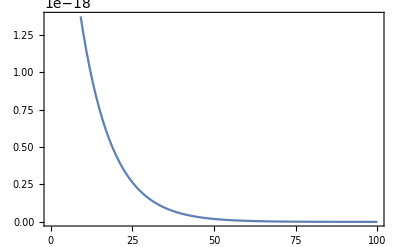

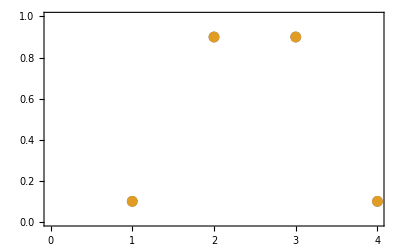

{{0.1,0.9,0.9,0.1}}

{{0.1,0.9,0.9,0.1}}

{{-1.13771×10^-12,7.26608×10^-12,1.258×10^-11,-2.13798×10^-12}}

```mathematica
w1=Table[
(*Lerne*)
Do[
eta=1;
netin =weights.(in[[i]]+Table[fnoise[0.0],{anzahlInput}]);
z = modulo[netin];
soll = out[[i]] * round[netin];
error = soll -netin;
diff=Outer[Times, eta/(anzahlInput+1)*error,Conjugate[in[[i]]]];
weights += diff;
,{i,1,4}];
(*Berechne Error*)
err=Transpose[toReal[out]]-Activ[weights.Transpose[in]];
1/2*(err.Transpose[err])[[1,1]]
,{epoche,100}];
ListPlot[w1,Frame->True,Joined->True](*Printe error*)
(*Schaue ob funktioniert*)
result=Table[Activ[weights.in[[i]]],{i,4}];
result=Transpose[result];
should=Table[toReal[out[[i]]],{i,4}];
should=Transpose[should];
ListPlot[{result[[1]],should[[1]]},Frame->True,PlotRange->{0,1}]
result
should
should-result
```